#### Область устойчивости метода Рунге-Кутты 2 порядка

k_1=f(t_n,y_n)
k_2=f(t_n+τ, y_n+τk_1)

```mathematica
f[y_]:=λ y
```

```mathematica
k1=f[Subscript[y, n]]
```

λ y_n

```mathematica
k2=f[Subscript[y, n]+τ k1]
```

λ (y_n+λ τ y_n)

```mathematica
eq=FullSimplify[(Subscript[y, n]+τ(1/2 k1+1/2 k2))/Subscript[y, n]/.λ->μ/τ]
```

1+μ+μ^2/2

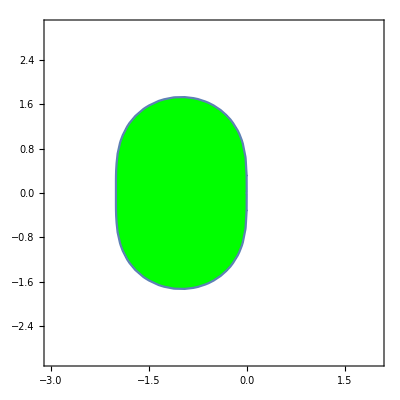

```mathematica
rk2=RegionPlot[Abs[eq/.μ->(x+ⅈ y)]<=1,{x,-6,6},{y,-6,6},Axes->True,PlotStyle->Green,PlotRange->{{-3,2},{-3,3}}]
```

#### Область устойчивости метода Рунге-Кутты 4 порядка

k_1=f(t_n,y_n)=λ y_n
k_2=f(t_n+τ/2, y_n+τ/2 k_1)
k_3=f(t_n+τ/2, y_n+τ/2 k_2)
k_4=f(t_n+τ,y_n+τ k_3)

```mathematica
f[y_]:=λ y
```

```mathematica
k1=f[Subscript[y, n]]
```

λ y_n

```mathematica
k2=f[Subscript[y, n]+τ/2 k1]
```

λ (y_n+1/2 λ τ y_n)

```mathematica
k3=f[Subscript[y, n]+τ/2 k2]
```

λ (y_n+1/2 λ τ (y_n+1/2 λ τ y_n))

```mathematica
k4=f[Subscript[y, n]+τ k3]
```

λ (y_n+λ τ (y_n+1/2 λ τ (y_n+1/2 λ τ y_n)))

```mathematica
eq=FullSimplify[(Subscript[y, n]+τ(1/6 k1+1/3 k2+1/3 k3+1/6 k4))/Subscript[y, n]/.λ->μ/τ]
```

1+μ+1/24 μ^2 (12+μ (4+μ))

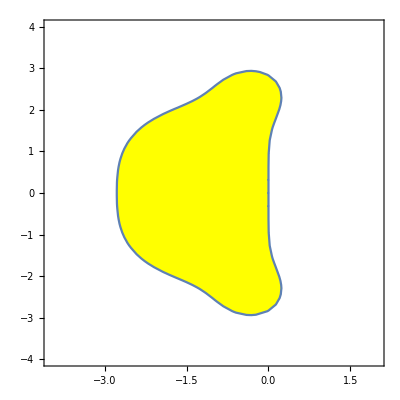

```mathematica
rk=RegionPlot[Abs[eq/.μ->(x+ⅈ y)]<=1,{x,-6,6},{y,-6,6},Axes->True,PlotStyle->Yellow,PlotRange->{{-4,2},{-4, 4}}]
```

Следовательно, метод не является А(α)-устойчивым.

#### Область устойчивости метода “прогноз-коррекция”

y_(n+1)^(0)=y_n+τ/24(55 f_n-59 f_(n-1)+37 f_(n-2)-9 f_(n-3)) 
f_(n+1)^(0)=f(t_(n+1),y_(n+1)^(0))
y_(n+1)=y_n+τ/24(9 f_(n+1)^(0)+19 f_n-5 f_(n-1)+f_(n-2))

f_(n+1)^(0)=λ (q^3+τ/24 λ(55 q^3-59 q^2+37q-9))=λ (q^3+μ/24(55 q^3-59 q^2+37q-9))
q^4=q^3+μ/24(9(q^3+μ/24(55 q^3-59 q^2+37q-9))+19 q^3-5 q^2+q)

```mathematica
FullSimplify[(q^4==q^3+1/24 μ (q-5 q^2+19 q^3+9 (q^3+1/24 (-9+37 q-59 q^2+55 q^3) μ)))/.{q->ⅇ^(ⅈ ϕ)},Assumptions->{ϕ>=0,ϕ<=2π}]
```

192 ⅇ^(4 ⅈ ϕ)+27 μ^2+ⅇ^(2 ⅈ ϕ) μ (40+177 μ)==ⅇ^(ⅈ ϕ) μ (8+111 μ)+ⅇ^(3 ⅈ ϕ) (192+μ (224+165 μ))

```mathematica
sols=Solve[%,μ]
```

{{μ→(4 (-ⅇ^(ⅈ ϕ)+5 ⅇ^(2 ⅈ ϕ)-28 ⅇ^(3 ⅈ ϕ)-√(ⅇ^(2 ⅈ ϕ)+314 ⅇ^(3 ⅈ ϕ)-1575 ⅇ^(4 ⅈ ϕ)+3176 ⅇ^(5 ⅈ ϕ)-3320 ⅇ^(6 ⅈ ϕ)+1980 ⅇ^(7 ⅈ ϕ))))/(3 (-9+37 ⅇ^(ⅈ ϕ)-59 ⅇ^(2 ⅈ ϕ)+55 ⅇ^(3 ⅈ ϕ)))},{μ→(4 (-ⅇ^(ⅈ ϕ)+5 ⅇ^(2 ⅈ ϕ)-28 ⅇ^(3 ⅈ ϕ)+√(ⅇ^(2 ⅈ ϕ)+314 ⅇ^(3 ⅈ ϕ)-1575 ⅇ^(4 ⅈ ϕ)+3176 ⅇ^(5 ⅈ ϕ)-3320 ⅇ^(6 ⅈ ϕ)+1980 ⅇ^(7 ⅈ ϕ))))/(3 (-9+37 ⅇ^(ⅈ ϕ)-59 ⅇ^(2 ⅈ ϕ)+55 ⅇ^(3 ⅈ ϕ)))}}

```mathematica
sol1=(μ/.sols[[1]])
sol2=(μ/.sols[[2]])
```

(4 (-ⅇ^(ⅈ ϕ)+5 ⅇ^(2 ⅈ ϕ)-28 ⅇ^(3 ⅈ ϕ)-√(ⅇ^(2 ⅈ ϕ)+314 ⅇ^(3 ⅈ ϕ)-1575 ⅇ^(4 ⅈ ϕ)+3176 ⅇ^(5 ⅈ ϕ)-3320 ⅇ^(6 ⅈ ϕ)+1980 ⅇ^(7 ⅈ ϕ))))/(3 (-9+37 ⅇ^(ⅈ ϕ)-59 ⅇ^(2 ⅈ ϕ)+55 ⅇ^(3 ⅈ ϕ)))

(4 (-ⅇ^(ⅈ ϕ)+5 ⅇ^(2 ⅈ ϕ)-28 ⅇ^(3 ⅈ ϕ)+√(ⅇ^(2 ⅈ ϕ)+314 ⅇ^(3 ⅈ ϕ)-1575 ⅇ^(4 ⅈ ϕ)+3176 ⅇ^(5 ⅈ ϕ)-3320 ⅇ^(6 ⅈ ϕ)+1980 ⅇ^(7 ⅈ ϕ))))/(3 (-9+37 ⅇ^(ⅈ ϕ)-59 ⅇ^(2 ⅈ ϕ)+55 ⅇ^(3 ⅈ ϕ)))

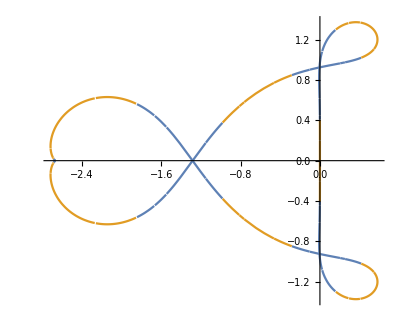

```mathematica
pec=ParametricPlot[{{Re[sol1],Im[sol1]},{Re[sol2],Im[sol2]}},{ϕ,0,2π}]
```

```mathematica
eq=(q^4==q^3+1/24 μ (q-5 q^2+19 q^3+9 (q^3+1/24 (-9+37 q-59 q^2+55 q^3) μ)))
```

q^4==q^3+1/24 μ (q-5 q^2+19 q^3+9 (q^3+1/24 (-9+37 q-59 q^2+55 q^3) μ))

```mathematica
(*устойчиво*)
NSolve[eq/.μ->-0.5,q]
```

{{q→-0.137294-0.416119 ⅈ},{q→-0.137294+0.416119 ⅈ},{q→0.304212},{q→0.601887}}

```mathematica
(*неустойчиво, левое сердечко*)
NSolve[eq/.μ->-2,q]
```

{{q→0.510504-0.203274 ⅈ},{q→0.510504+0.203274 ⅈ},{q→0.541579-1.25287 ⅈ},{q→0.541579+1.25287 ⅈ}}

```mathematica
(*неустойчиво, за пределами фигуры*)
NSolve[eq/.μ->-2.75,q]
```

{{q→0.649152},{q→0.78034-0.422336 ⅈ},{q→0.78034+0.422336 ⅈ},{q→2.08086}}

```mathematica
(*неустойчиво*)
NSolve[eq/.μ->1,q]
```

{{q→0.0349808-0.437198 ⅈ},{q→0.0349808+0.437198 ⅈ},{q→0.272398},{q→2.68368}}

```mathematica
(*неустойчиво, правая петелька*)
NSolve[eq/.μ->0.3+1.2ⅈ,q]
```

{{q→-0.788942+1.20742 ⅈ},{q→0.215581-0.329611 ⅈ},{q→0.31902+0.109034 ⅈ},{q→0.444184+1.0319 ⅈ}}

Метод условно устойчив. В область устойчивости входит только “стрелочка” в левой полуплоскости.

#### Область устойчивости метода Адамса-Башфорта 4 порядка

```mathematica
eq2=(q^4==q^3+μ/24(55 q^3-59 q^2+37q-9))
```

q^4==q^3+1/24 (-9+37 q-59 q^2+55 q^3) μ

```mathematica
FullSimplify[eq2/.{q->ⅇ^(ⅈ ϕ)},Assumptions->{ϕ>=0,ϕ<=2π}]
```

24 ⅇ^(4 ⅈ ϕ)+9 μ+59 ⅇ^(2 ⅈ ϕ) μ==37 ⅇ^(ⅈ ϕ) μ+ⅇ^(3 ⅈ ϕ) (24+55 μ)

```mathematica
solsAdams=Solve[%,μ]
```

{{μ→(24 ⅇ^(3 ⅈ ϕ) (-1+ⅇ^(ⅈ ϕ)))/(-9+37 ⅇ^(ⅈ ϕ)-59 ⅇ^(2 ⅈ ϕ)+55 ⅇ^(3 ⅈ ϕ))}}

```mathematica
solAdams=μ/.solsAdams[[1]]
```

(24 ⅇ^(3 ⅈ ϕ) (-1+ⅇ^(ⅈ ϕ)))/(-9+37 ⅇ^(ⅈ ϕ)-59 ⅇ^(2 ⅈ ϕ)+55 ⅇ^(3 ⅈ ϕ))

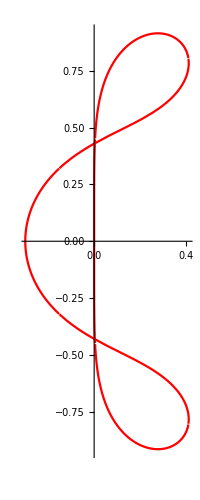

```mathematica
adams=ParametricPlot[{Re[solAdams],Im[solAdams]},{ϕ,0,2π},PlotStyle->Red]
```

```mathematica
(*устойчиво*)
NSolve[eq2/.μ->-0.1,q]
```

{{q→-0.523354},{q→0.194673-0.203202 ⅈ},{q→0.194673+0.203202 ⅈ},{q→0.904841}}

```mathematica
(*неустойчиво*)
NSolve[eq2/.μ->-0.4,q]
```

{{q→-1.21984},{q→0.314315-0.288967 ⅈ},{q→0.314315+0.288967 ⅈ},{q→0.674545}}

```mathematica
(*неустойчиво, правая петелька*)
NSolve[eq2/.μ->0.2+0.7ⅈ,q]
```

{{q→0.0182545+1.23413 ⅈ},{q→0.2098-0.466005 ⅈ},{q→0.367895+0.0549566 ⅈ},{q→0.862383+0.781089 ⅈ}}

Метод условно устойчив. В область устойчивости входит только левый ”полукруг”.

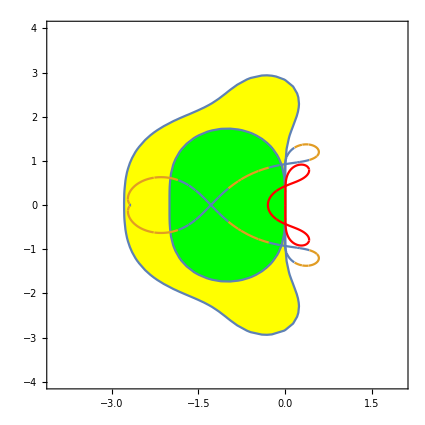

```mathematica
Show[rk,rk2, pec, adams]
```